```mathematica
elementList={"Sc"->1,"Ti"->2,"V"->3,"Cr"->4,"Mn"->5,"Fe"->6,"Co"->7,"Ni"->8,"Cu"->9,"Zn"->10,"Y"->11,"Zr"->12,"Nb"->13,"Mo"->14,"Tc"->15,"Ru"->16,"Rh"->17,"Pd"->18,"Ag"->19,"Hf"->20,"Ta"->21,"W"->22,"Re"->23,"Os"->24,"Ir"->25,"Pt"->26,"Au"->27};
elements=List@@@elementList//Transpose//First;
targets = {ORR -> -1.51, CORedCO -> -1.20, ORedCO -> -1.25};

myPrint[list_]:=ToString[Row[{"(",Row[NumberForm[#,{4,3}]&/@list," "],")"}]]
```

## Parse Data:

```mathematica
data=Import["/home/marco/fridbDemo/allresults.json"];
```

Parse 38 atom NP oxygen binding energy:

```mathematica
atoms32=Select[data,StringCases[#[[1]],"32"]≠{}&];
atoms32Binding=Select[atoms32,StringCases[#[[1]],"Binding"]≠{}&];
dataall={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms32Binding)/.elementList;
tab=Table[Cases[dataall,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
smallBindingTable = Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;
```

Parse 79 atom NP oxygen:

```mathematica
atoms79=Select[data,StringCases[#[[1]],"60"]≠{}&];
atoms79Binding=Select[atoms79,StringCases[#[[1]],"Binding"]≠{}&];
dataall79={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms79Binding)/.elementList;
tab=Table[Cases[dataall79,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
bigBindingTable = Table[With[{x=Cases[dataall79,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;
```

Parse 79 atom NP Segregation Energy

```mathematica
atoms79Segregation=Select[atoms79,StringCases[#[[1]],"Segregation Energy"~~EndOfString]≠ {}&];
dataSegFormat={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms79Segregation)/.elementList;
bigSegTable = Table[With[{x=Cases[dataSegFormat,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];

atoms79SegregationOxygen=Select[atoms79,StringCases[#[[1]],"Segregation Energy With Oxygen"~~EndOfString]≠ {}&];
dataSegWithOxygenFormat={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms79SegregationOxygen)/.elementList;
bigSegTableOxygen = Table[With[{x=Cases[dataSegWithOxygenFormat,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
atoms79Segregation
atoms79SegregationOxygen
```

{19/Ag/60/Ag/Segregation Energy→{a1→19,a2→60,M1→Ag,M2→Ag,metadata→19Ag@60Ag_sbn: -180.818365 by mdh2736<br> 19Ag@60Ag_bnp: -180.818365 by mdh2736,result→1.00000079328e-08,result_type→Segregation Energy,url→{s1→./database/19Ag@60Ag_sbn/e833e5d0fbb0940d4dd51abdbfbdac75/CONTCAR,s2→./database/19Ag@60Ag_bnp/1fe2c8905bb42f6a36210bc1e63cb6c2/CONTCAR},username→mdh2736},«545»,19/Zr/60/Zr/Segregation Energy→{a1→19,«7»,username→mdh2736}}

{19/Ag/60/Ag/Segregation Energy With Oxygen→{a1→19,a2→60,M1→Ag,M2→Ag,metadata→19Ag@60Ag_sno: -186.553713 by mdh2736<br> 19Ag@60Ag_npo: -186.552826 by mdh2736,result→-0.000887820000003,result_type→Segregation Energy With Oxygen,url→{s1→./database/19Ag@60Ag_sno/d902e7a83be792af0f2b6e56ce19da9e/CONTCAR,s2→./database/19Ag@60Ag_npo/d2e690fba6f7c101d1fe19ea05306c93/CONTCAR},username→mdh2736},«628»,19/Zr/60/Zn/Segregation Energy With Oxygen→{«1»}}

```mathematica
atoms38Segregation=Select[atoms32,StringCases[#[[1]],"Segregation Energy"~~EndOfString]≠ {}&];
data38SegFormat={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms38Segregation)/.elementList;
smallSegTable = Table[With[{x=Cases[data38SegFormat,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];

atoms38SegregationOxygen=Select[atoms32,StringCases[#[[1]],"Segregation Energy With Oxygen"~~EndOfString]≠ {}&];
data38SegWithOxygenFormat={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms38SegregationOxygen)/.elementList;
smallSegTableOxygen = Table[With[{x=Cases[data38SegWithOxygenFormat,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
atoms38Segregation
atoms38SegregationOxygen
```

{6/Ag/32/Ag/Segregation Energy→{a1→6,a2→32,M1→Ag,M2→Ag,metadata→6Ag@32Ag_sbn: -82.091633 by mdh2736<br> 6Ag@32Ag_bnp: -82.091633 by mdh2736,result→0.0,result_type→Segregation Energy,url→{s1→./database/6Ag@32Ag_sbn/ab2891b85fd8b30fc84ceb37d6b0adf3/CONTCAR,s2→./database/6Ag@32Ag_bnp/1247fe7ac3d788a30c43c5402d420608/CONTCAR},username→mdh2736},6/Ag/32/Au/Segregation Energy→{«1»},«748»,6/Zr/32…n Energy→«1»,6/Zr/32/Zr/Segregation Energy→{a1→6,a2→32,«6»,username→mdh2736}}

{6/Ag/32/Ag/Segregation Energy With Oxygen→{a1→6,a2→32,M1→Ag,M2→Ag,metadata→6Ag@32Ag_sno: -87.881337 by mdh2736<br> 6Ag@32Ag_npo: -87.926179 by mdh2736,result→0.04484208,result_type→Segregation Energy With Oxygen,url→{s1→./database/6Ag@32Ag_sno/84fa8e0b27195b30e35b597c6fe3edf5/CONTCAR,s2→./database/6Ag@32Ag_npo/85fc9fe6fabc5f98f9e05c4294ca4411/CONTCAR},username→mdh2736},«706»,6/Zr/32/Zr/Segregation Energy With Oxygen→{a1→6,«7»,username→m…6}}

## Make Matrix Plots:

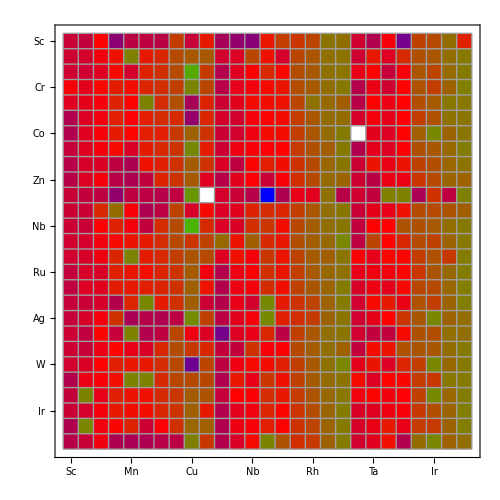

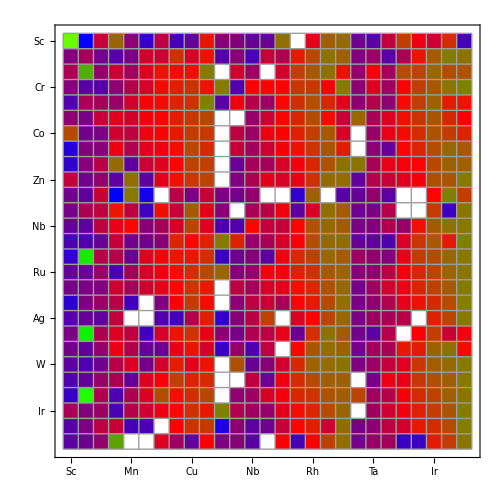

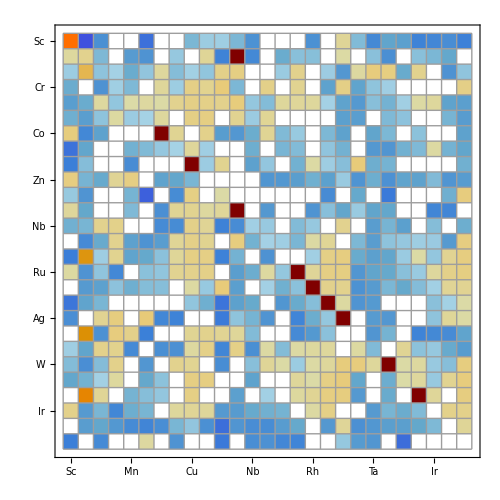

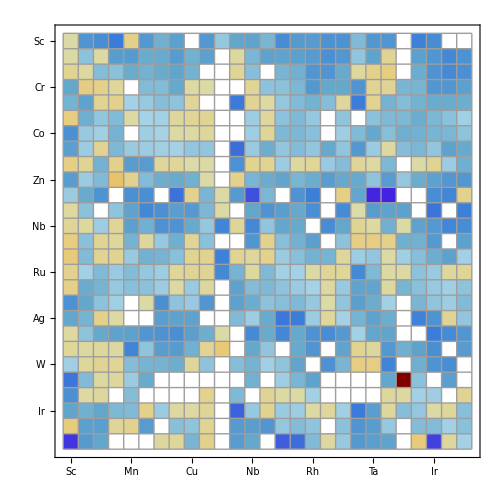

```mathematica
MatrixPlot[smallBindingTable,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]

MatrixPlot[bigBindingTable,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]

MatrixPlot[bigSegTable, Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]

MatrixPlot[bigSegTableOxygen, Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]
```

## Make Bar Charts:

### These statements are used to filter out spurious binding energies. Then nanoparticle removed has its corresponding label removed, so that the bar chart bars and their labes line up correctly

{}

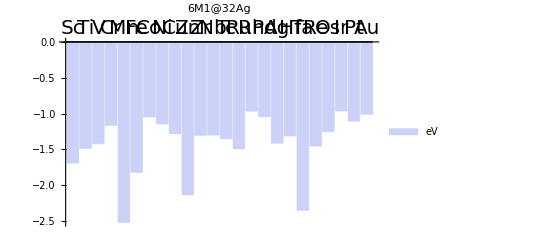

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

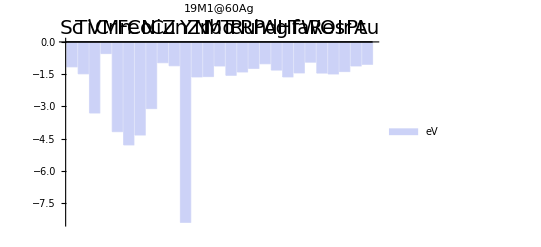

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

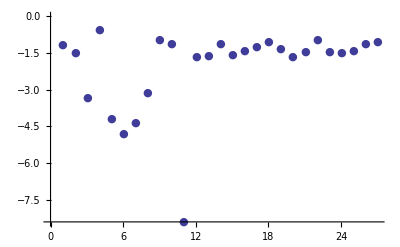

-Graphics-

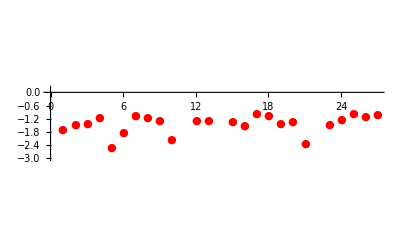

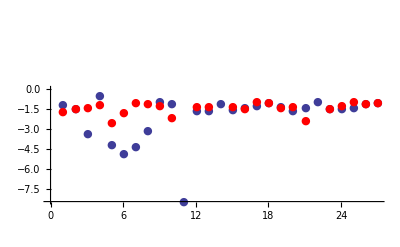

{0.528839,0.00008181,-1.8915,0.6229,-1.66226,-2.97975,-3.29121,-1.96083,0.313333,1.02347,1.6646,-0.328496,-0.314616,-5.48928,-0.205317,0.0908144,-0.267932,0.0252885,0.100085,-0.317968,0.904503,-5.36616,0.00134848,-0.242626,-0.417037,-0.0155537,-0.0349103}

```mathematica
placeholder =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
removedElementsPos = Position[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
newElementsSmall = Delete[elements, # & /@removedElementsPos] ;

placeholder2 =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,bigBindingTable[[All,19]] ],0];
removedElementsPos2 = Position[Map[ If[# >0 || # <-10,0,#] &,bigBindingTable[[All,19]] ],0]
newElementsBig = Delete[elements, # & /@removedElementsPos2] ;
newElementsSmall == newElementsBig;
Delete[placeholder2, 1] ;

BarChart[placeholder,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsSmall,Above]},PlotLabel->Style["6M1@32Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements

BarChart[placeholder2,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsBig,Above]},PlotLabel->Style["19M1@60Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements
p1 = ListPlot[{#} & @bigBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}]


Show[p1,Graphics[{Red,elements}] ]
p2 = ListPlot[smallBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}, PlotStyle -> Red]
Show[p1,p2]
bigBindingTable[[All, 19]] - smallBindingTable[[All,19]]
```

## Ag, Pt Dot Chart

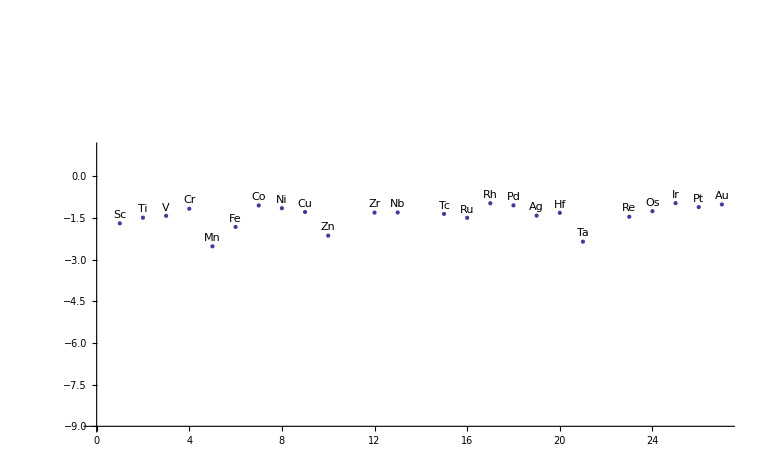

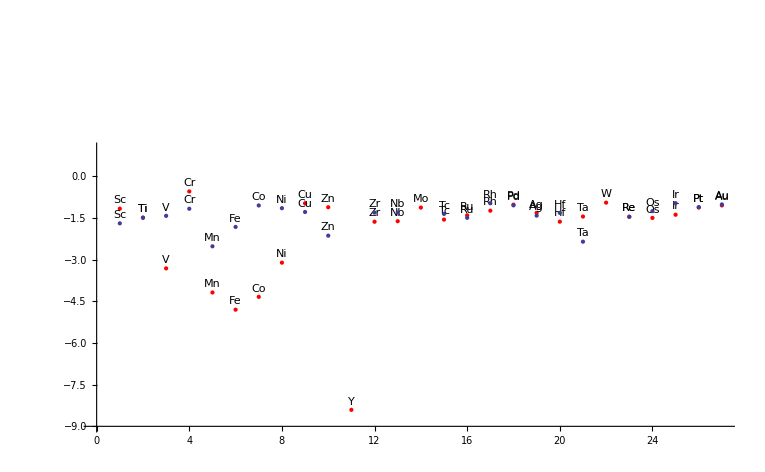

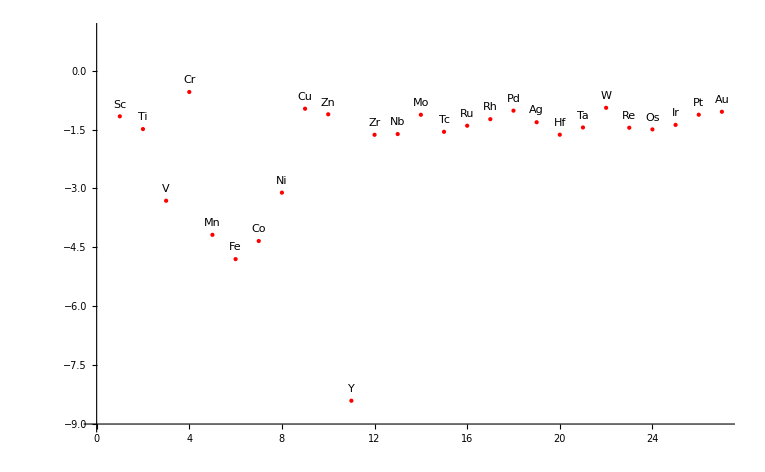

-Graphics-

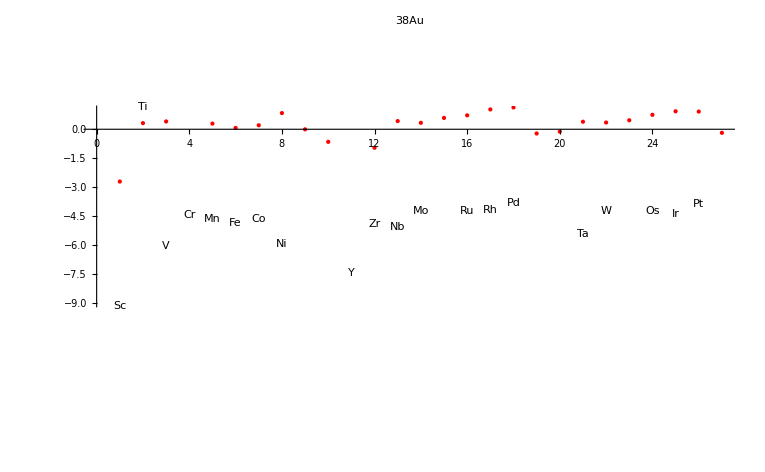

```mathematica
dataPlot1=ListPlot[smallBindingTable[[All,19]],PlotStyle->PointSize->Large,AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}];
labels1=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@smallBindingTable[[All,19]]],smallBindingTable[[All,19]]}];
Show[dataPlot1,Graphics[labels1]]

dataPlot2=ListPlot[bigBindingTable[[All,19]],PlotStyle->{Red,PointSize->Large},AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}];
labels2=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@bigBindingTable[[All,19]]],bigBindingTable[[All,19]]}];

dataPlot3=ListPlot[smallBindingTable[[All,27]] - ORR /. targets,PlotStyle->{Red,PointSize->Large},PlotRange->{Automatic,{-9,1}},PlotLabel -> "38Au", AxesOrigin->{0,0} ];
labels3=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@smallBindingTable[[All,27]]],smallBindingTable[[All,5]]}];

Show[dataPlot2,Graphics[labels2], dataPlot1, Graphics[labels1]]
Show[dataPlot2,Graphics[labels2]]
Show[dataPlot1, Graphics[labels1]]
Show[dataPlot3,Graphics[labels3]]
```

```mathematica
lst = Delete[lst,3]
```

{19→2.85077,27→2.8549,4→2.84034,9→2.81286,6→2.8282,20→2.96446,25→2.83727,5→2.83799,14→2.84114,13→2.91995,8→2.83038,24→2.84655,18→2.84554,26→2.84533,23→2.86048,17→2.84004,16→2.84042,1→2.92212,21→2.91318,15→2.85081,2→2.88824,3→2.87623,22→2.89723,11→2.96313,10→2.84196,12→2.97649}

## Average Bond Length Plots:

```mathematica
bondLenData = Import["/home/marco/fridbDemo/avgbondlen.json"] /. elementList;
```

Get Bond Length for bnp 38 nanoparticles

```mathematica
lst=  "bnp" /. bondLenData[[1]];
lst = "38" /. lst;

lst = Delete[lst,3];
lst = Delete[lst,8];
bnp38BL = Table[x, {x,1,27}] /. lst;
```

Get Bond Length for bnp 79 nanoparticles:

```mathematica
lst2=  "bnp" /. bondLenData[[1]];
lst2 = "79" /. lst2;
lst2 = Delete[lst,3];
lst2 = Delete[lst,8];
bnp79BL = Table[x, {x,1,27}] /. lst2; 

bondLenData[[1]]
```

bnp→{38→{19→2.85077,27→2.8549,Cd→2.88438,7→2.8297,4→2.84034,9→2.81286,6→2.8282,20→2.96446,Hg→2.87532,25→2.83727,5→2.83799,14→2.84114,13→2.91995,8→2.83038,24→2.84655,18→2.84554,26→2.84533,23→2.86048,17→2.84004,16→2.84042,1→2.92212,21→2.91318,15→2.85081,2→2.88824,3→2.87623,22→2.89723,11→2.96313,10→2.84196,12→2.97649},79→{19→2.87259,27→2.87463,Cd→2.88172,7→2.78466,4→2.82841,9→2.80938,6→2.77798,20→3.00874,25→2.81191,5→2.80125,14→2.82716,13→2.83941,8→2.7879,24→2.79815,18→2.82765,26→2.83002,23→2.8378,17→2.81816,16→2.80325,1→2.9742,21→2.96703,15→2.82528,2→2.8858,3→2.80727,22→2.83959,11→2.96012,10→2.85065}}

Make Plots of Bond Length data:

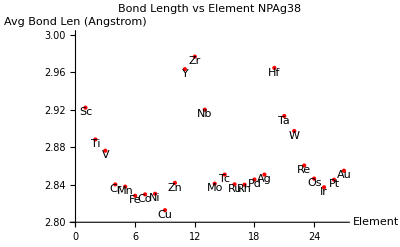

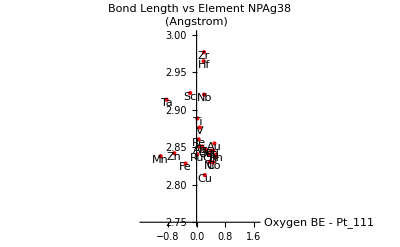

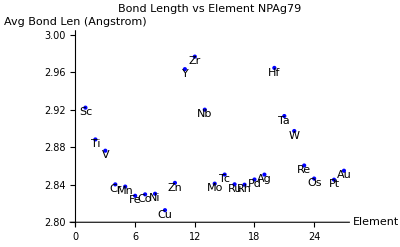

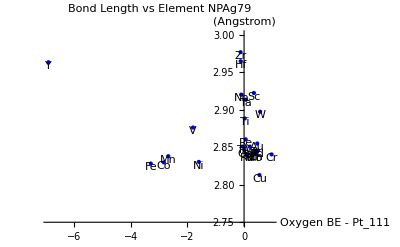

```mathematica
bondLenVsElement38 = ListPlot[bnp38BL, PlotStyle -> {Red, PointSize -> Large},PlotRange -> {2.80, 3},  PlotLabel -> "Bond Length vs Element NPAg38", AxesLabel->{"Element", "Avg Bond Len (Angstrom)"}];
bondLenVsElementLabels38=MapThread[Text[#1,{#2,#3-0.005}]&,{elements,Range[Length@bnp38BL], bnp38BL}];

bondLenVsBe38data = Partition[#,2] & @Riffle[#1, #2] & @@{smallBindingTable[[All,19]] - ORR /. targets, bnp38BL};
bondLenVsBe38=ListPlot[bondLenVsBe38data, PlotStyle->{Red,PointSize->Large}, PlotRange->{2.75, 3}, PlotLabel -> "Bond Length vs Element NPAg38", AxesLabel->{"Oxygen BE - Pt_111", "(Angstrom)"}];
bondLenVsBeLabels38=MapThread[Text[#1,{#2 ,#3- 0.005}]&,{elements,smallBindingTable[[All,19]] - ORR /. targets, bnp38BL}];

bondLenVsElement79 = ListPlot[bnp79BL, PlotStyle -> {Blue, PointSize -> Large},PlotRange -> {2.80, 3},  PlotLabel -> "Bond Length vs Element NPAg79", AxesLabel->{"Element", "Avg Bond Len (Angstrom)"}];
bondLenVsElementLabels79=MapThread[Text[#1,{#2,#3-0.005}]&,{elements,Range[Length@bnp79BL], bnp79BL}];

bondLenVsBe79data = Partition[#,2] & @Riffle[#1, #2] & @@{bigBindingTable[[All,19]] - ORR /. targets, bnp79BL};
bondLenVsBe79=ListPlot[bondLenVsBe79data, PlotStyle->{Blue,PointSize->Large}, PlotRange->{2.75, 3}, PlotLabel -> "Bond Length vs Element NPAg79", AxesLabel->{"Oxygen BE - Pt_111", "(Angstrom)"}];
bondLenVsBeLabels79=MapThread[Text[#1,{#2 ,#3- 0.005}]&,{elements,bigBindingTable[[All,19]] - ORR /. targets, bnp79BL}];




Show[bondLenVsElement38, Graphics[bondLenVsElementLabels38] ]
Show[bondLenVsBe38, Graphics[bondLenVsBeLabels38] ]

Show[bondLenVsElement79, Graphics[bondLenVsElementLabels79] ]
Show[bondLenVsBe79, Graphics[bondLenVsBeLabels79] ]
```

## Filter Particles:

```mathematica
assignNums[sege_] := If[ sege[[1]] ≥ 0 && sege[[2]] ≥ 0, 1, 
If[ Xor[sege[[1]] ≥ 0, sege[[2]] ≥ 0], 2,
If[ sege[[1]] ≤ 0 &&  sege[[2]] ≤ 0, -1]
]
]
segColor = {2->Yellow, 1 -> Green, -1 -> Red}

getSmallSeg[core_,shell_] :={smallSegTable[[core, shell ]] , smallSegTableOxygen[[core, shell]]}
getBigSeg[core_,shell_] :={bigSegTable[[core, shell ]] , bigSegTableOxygen[[core, shell]]}

joinNames[el1_, el2_] := Table[el1[[i]]<>"@"<>el2[[i]], {i, Length[el1]}]
```

{2→RGBColor[1,1,0],1→RGBColor[0,1,0],-1→RGBColor[1,0,0]}

{{idealORRSmall,Sc,Pd,0.0381286},{idealORRSmall,Ti,Ag,0.0234839},{idealORRSmall,Mn,Rh,-0.0418618},{idealORRSmall,Fe,Pt,-0.0379584},{idealORRSmall,Cu,Au,-0.00495028},{idealORRSmall,Ru,Ag,0.0179224},{idealORRSmall,W,Pd,-0.0176639}}

{{idealORRBig,Sc,Pd,-0.00103932},{idealORRBig,Ti,Ag,0.0235657},{idealORRBig,Mn,Ir,0.0309183},{idealORRBig,Cu,Au,0.0284615},{idealORRBig,Tc,Ag,-0.046035},{idealORRBig,Re,Pd,-0.0441911},{idealORRBig,Re,Pt,0.0172549},{idealORRBig,Os,Ag,0.015038},{idealORRBig,Os,Pt,0.0314884}}

{{1,18},{2,19},{5,17},{6,26},{9,27},{16,19},{22,18}}

{2,2,2,2,-1,2,2}

{{1,18},{2,19},{5,25},{9,27},{15,19},{23,18},{23,26},{24,19},{24,26}}

{2,2,2,-1,1,1,2,1,1}

{{1,18,2},{2,19,2},{5,17,2},{6,26,2},{9,27,-1},{16,19,2},{22,18,2}}

{{1,18,2},{2,19,2},{5,25,2},{9,27,-1},{15,19,1},{23,18,1},{23,26,2},{24,19,1},{24,26,1}}

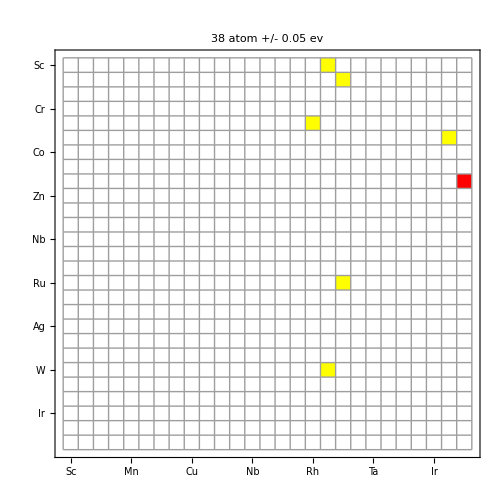

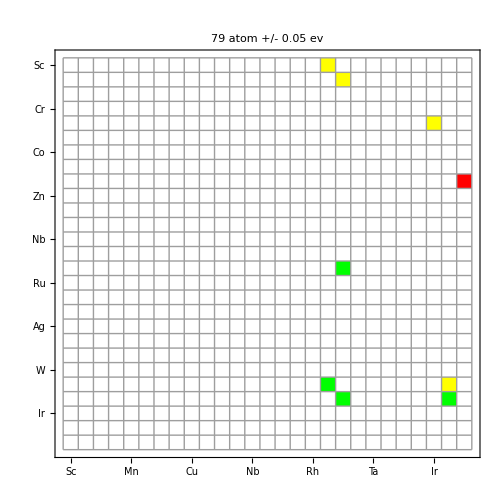

```mathematica
idealORRSmall = Replace[smallBindingTable- (ORR) /. targets,a_/;Abs[a]≥0.05->0,{2}] ;
idealORRBig = Replace[bigBindingTable- (ORR) /. targets ,a_/;Abs[a] ≥0.05->0,{2}];


info[tbl_]:=With[{s=SparseArray[tbl]},ArrayPad[Append@@@Transpose[{s["NonzeroPositions"],s["NonzeroValues"]}],{0,{1,0}},ToString@Unevaluated@tbl]]

SetAttributes[info,HoldFirst]


idealOrrSmallDisp = DeleteCases[  info[idealORRSmall]/.  Reverse /@ elementList,{__,"no"}]
idealOrrBigDisp = DeleteCases[  info[idealORRBig]/.  Reverse /@ elementList,{__,"no"}]

idealSmallPairs = {#2, #3} & @@@ DeleteCases[  info[idealORRSmall]/. elementList,{__,"no"}]
idealSmallSeglst =assignNums[getSmallSeg[#1,#2]]& @@@ idealSmallPairs

idealBigPairs = {#2, #3} & @@@ DeleteCases[  info[idealORRBig]/.elementList,{__,"no"}]
idealBigSeglst =assignNums[getBigSeg[#1,#2]]& @@@ idealBigPairs

myDataIdealSmallSeglst = Table[Insert[idealSmallPairs[[i]],idealSmallSeglst[[i]],3],{i,Length[idealSmallSeglst] }]
myDataIdealBigSeglst = Table[Insert[idealBigPairs[[i]],idealBigSeglst[[i]],3],{i,Length[idealBigSeglst] }]

MatrixPlot[ SparseArray[ # ->  myDataIdealSmallSeglst[[All,3]], {27,27} ] & @ idealSmallPairs,ColorRules-> segColor,Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500, PlotLabel->"38 atom +/- 0.05 ev"]

MatrixPlot[ SparseArray[ # ->  myDataIdealBigSeglst[[All,3]], {27, 27} ] & @ idealBigPairs,ColorRules-> segColor,Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500,  PlotLabel->"79 atom +/- 0.05 ev"]
```

#### Graeme’s Suggested Stability Plots

```mathematica
idealSmallSege =getSmallSeg[#1,#2]& @@@ idealSmallPairs
idealBigSege = getBigSeg[#1, #2] & @@@ idealBigPairs
```

{{0,-1.37075},{1.08015,-1.39307},{2.15467,-0.33573},{0.477874,-0.884866},{-0.298466,-0.384991},{1.16092,-0.227978},{1.47873,-2.01226}}

{{0,-3.00314},{0.0571093,-2.42311},{0.217773,-0.951889},{-1.06271,-0.834213},{2.41305,0.340741},{1.44036,0},{0.51778,-1.64195},{2.48285,0},{0,0}}

{{Sc,Pd,{0,-1.37075},0.0381286},{Ti,Ag,{1.08015,-1.39307},0.0234839},{Mn,Rh,{2.15467,-0.33573},-0.0418618},{Fe,Pt,{0.477874,-0.884866},-0.0379584},{Cu,Au,{-0.298466,-0.384991},-0.00495028},{Ru,Ag,{1.16092,-0.227978},0.0179224},{W,Pd,{1.47873,-2.01226},-0.0176639}}

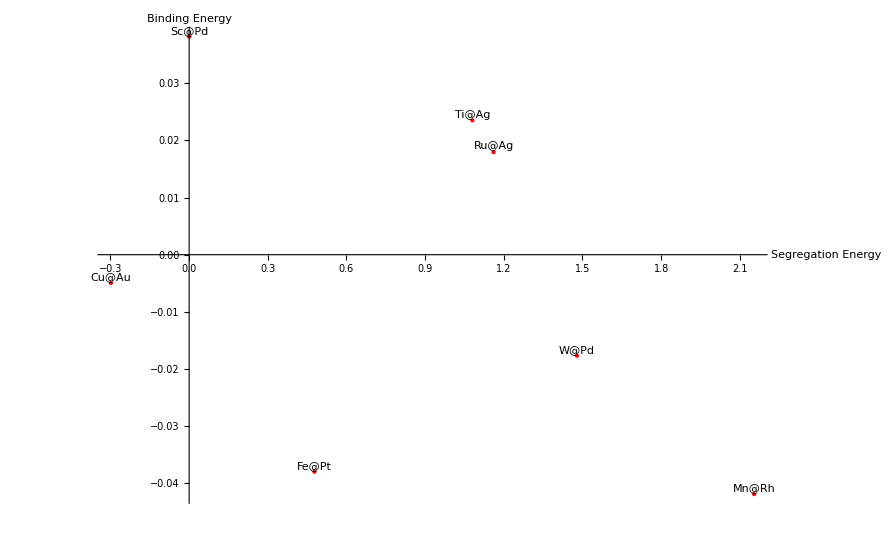

{Text[Sc@Pd,{0,0.0391286}],Text[Ti@Ag,{1.08015,0.0244839}],Text[Mn@Rh,{2.15467,-0.0408618}],Text[Fe@Pt,{0.477874,-0.0369584}],Text[Cu@Au,{-0.298466,-0.00395028}],Text[Ru@Ag,{1.16092,0.0189224}],Text[W@Pd,{1.47873,-0.0166639}]}

{Text[Sc,{1,-9.1589}],Text[Ti,{2,1.16011}],Text[V,{3,-6.07304}],Text[Cr,{4,-4.45426}],Text[Mn,{5,-4.67377}],Text[Fe,{6,-4.83699}],Text[Co,{7,-4.67284}],Text[Ni,{8,-5.94834}],Text[Cu,{9,-17.0761}],Text[Zn,{10,-14.8995}],Text[Y,{11,-7.42887}],Text[Zr,{12,-4.8863}],Text[Nb,{13,-5.07438}],Text[Mo,{14,-4.25823}],Text[Tc,{15,2.85369}],Text[Ru,{16,-4.25508}],Text[Rh,{17,-4.20586}],Text[Pd,{18,-3.83434}],Text[Ag,{19,-19.6224}],Text[Hf,{20,2.85403}],Text[Ta,{21,-5.44707}],Text[W,{22,-4.24741}],Text[Re,{23,3.15118}],Text[Os,{24,-4.25521}],Text[Ir,{25,-4.40117}],Text[Pt,{26,-3.87768}],Text[Au,{27,-18.2632}]}

```mathematica
stabilityIdealSmallSeglst = Table[Insert[idealSmallPairs[[i]] /. Reverse /@ elementList ,idealSmallSege[[i]],3],{i,Length[idealSmallSege] }];

stabilityIdealSmallSeglst = Table[Insert[stabilityIdealSmallSeglst[[i]],idealOrrSmallDisp[[i,4]],4],{i,Length[stabilityIdealSmallSeglst] }]


graemeSmall = ListPlot[Partition[Riffle[stabilityIdealSmallSeglst[[All, 3,1]], stabilityIdealSmallSeglst[[All, 4]] ], 2],PlotStyle -> { Red, PointSize->Medium}, AxesLabel-> {"Segregation Energy", "Binding Energy"} ];

coreShell = joinNames[#1, #2] & @@{stabilityIdealSmallSeglst[[All,1]], stabilityIdealSmallSeglst[[All,2]]};
labels4=MapThread[Text[#1,{#2,#3+0.001}]&,{coreShell,stabilityIdealSmallSeglst[[All,3,1]],stabilityIdealSmallSeglst[[All,4]] }];

Show[graemeSmall, Graphics[labels4]]

labels4
labels3
```

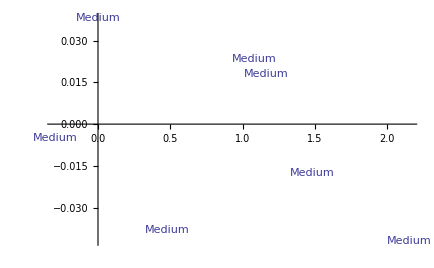

-Graphics-

Syntax::tsntxi: "[[i, 4]]" is incomplete; more input is needed."<>"

Syntax::sntxi: Incomplete expression; more input is needed "".

### Filter For Tunable Particles:

```mathematica
returnValueTest[row_, col_,tbl_] := tbl[[row,col]] 
tables = { smallBindingTable, bigBindingTable};
```

#### Filter Small Particles:

```mathematica
returnValue[row_,col_,myTable_]:=myTable[[row,col]];
filter =Replace[smallBindingTable,a_/;Abs[a]≥10->666,{2}]- (-1.51)/.targets; (*set any spurious values to zero *)
(* A particle is tunable if its pure form (located on the diagnols of the table) is opposite in sign to its core@shell parnter *)
d=Sign@Diagonal@filter;

tunablePairs=Position[(filterᵀ d)ᵀ,_?Negative]/.Reverse/@elementList;
pairEnergy=returnValue[#1,#2, smallBindingTable]&@@{#1,#2}&@@@Position[(filterᵀ d)ᵀ,_?Negative];
tempVar=Partition[Riffle[tunablePairs,pairEnergy],2];
filterImposs=Replace[tempVar,a_/;Abs[a]>5->666,{2}];

Cases[filterImposs,{x_,y_}/;x[[2]]≠("Zn")];
Cases[%,{x_,y_}/;x[[2]]≠("Zr")];
Partition[Riffle[ %[[All,1]],%[[All,2]] ],2];
tunableSmall = DeleteCases[%,{x_,y_}/;y==0];

DeleteDuplicates[ Flatten[ tunableSmall[[All,1]] ] ];

pure = Extract[ smallBindingTable, Partition[Riffle[ tunableSmall[[All,1,2]] /. elementList , tunableSmall[[All,1,2]] /. elementList],2]];

(*ratio = idealRatio[finalTunableBig[[All,2]], -1.51, finalTunableBig[[All,3]] ]; *)tunableSmall = ArrayFlatten[{{tunableSmall,Transpose[{pure}]}}];

ratio = (tunableSmall[[All,2]] + 1.51)/(tunableSmall[[All,2]] - tunableSmall[[All,3]]);

finalTunableSmall= ArrayFlatten[{{tunableSmall,Transpose[{ratio}]}}];

finalTunableSmall = DeleteCases[finalTunableSmall,{x_,y_,z_,f_}/;z==666];
finalTunableSmall = DeleteCases[finalTunableSmall,{x_,y_,z_,f_}/;y==666];

Partition[Riffle[finalTunableSmall[[All,1]], finalTunableSmall[[All,4]]],2] ;

finalTunableadj = {#1,#2+1.51,#3+1.51, #4 } &@@@finalTunableSmall[[All,1;;]];
finalTunableadj/. {{l1_,l2_},x1_ ,x2_ ,_}:>Thread@Labeled[Thread@{l2/.elementList,{x1,x2}},{l1,l2}];
SortBy[ finalTunableadj /. elementList,#[[2]]&] /. Reverse /@ elementList;
myPrint[finalTunableadj[[All,1]]]
```

({Sc, Pd} {Sc, Ag} {Ti, Mn} {Ti, Au} {V, Au} {Cr, Cu} {Cr, Au} {Mn, Fe} {Mn, Ag} {Mn, Pt} {Mn, Au} {Fe, Ag} {Fe, Au} {Co, Au} {Ni, Cu} {Ni, Au} {Zn, Ag} {Y, W} {Y, Re} {Y, Au} {Nb, Au} {Mo, Au} {Tc, Mn} {Tc, Au} {Ru, Au} {Rh, Au} {Pd, Fe} {Pd, Mo} {Pd, Au} {Ag, Ir} {Hf, Mn} {Ta, Ag} {Ta, Au} {W, Ir} {W, Au} {Re, Mn} {Re, Fe} {Re, Pt} {Re, Au} {Os, Ti} {Os, Ir} {Os, Au} {Ir, Au} {Pt, Ti} {Pt, Au} {Au, Cu} {Au, Mo} {Au, Ir})

#### Function to get both Segregation energies for particles

### Matrix Plot for Tunable Small

{{1,18},{1,19},{2,5},{2,27},{3,27},{4,9},{4,27},{5,6},{5,19},{5,26},{5,27},{6,19},{6,27},{7,27},{8,9},{8,27},{10,19},{11,22},{11,23},{11,27},{13,27},{14,27},{15,5},{15,27},{16,27},{17,27},{18,6},{18,14},{18,27},{19,25},{20,5},{21,19},{21,27},{22,25},{22,27},{23,5},{23,6},{23,26},{23,27},{24,2},{24,25},{24,27},{25,27},{26,2},{26,27},{27,9},{27,14},{27,25}}

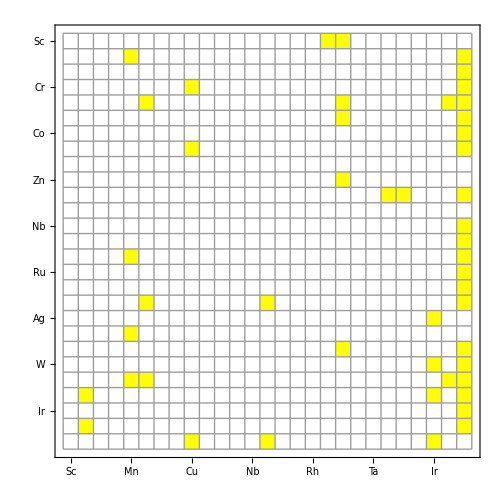

{2,-1,-1,-1,2,2,2,2,1,2,2,2,2,2,2,-1,-1,-1,2,2,2,-1,1,2,2,2,-1,-1,2,-1,2,2,2,2,2,1,2,2,2,-1,2,2,2,-1,1,-1,2,-1}

{{1,18,2},{1,19,-1},{2,5,-1},{2,27,-1},{3,27,2},{4,9,2},{4,27,2},{5,6,2},{5,19,1},{5,26,2},{5,27,2},{6,19,2},{6,27,2},{7,27,2},{8,9,2},{8,27,-1},{10,19,-1},{11,22,-1},{11,23,2},{11,27,2},{13,27,2},{14,27,-1},{15,5,1},{15,27,2},{16,27,2},{17,27,2},{18,6,-1},{18,14,-1},{18,27,2},{19,25,-1},{20,5,2},{21,19,2},{21,27,2},{22,25,2},{22,27,2},{23,5,1},{23,6,2},{23,26,2},{23,27,2},{24,2,-1},{24,25,2},{24,27,2},{25,27,2},{26,2,-1},{26,27,1},{27,9,-1},{27,14,2},{27,25,-1}}

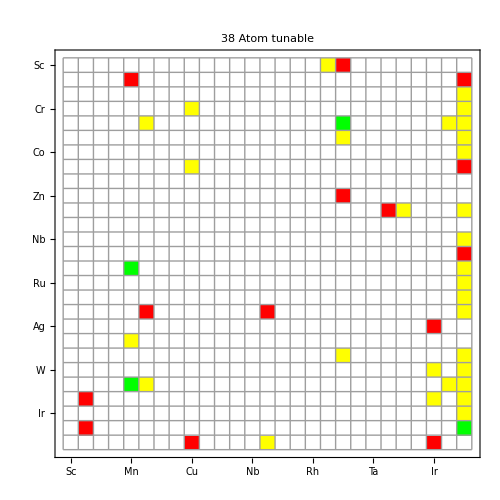

{{1,18},{1,19},{2,5},{2,27},{3,27},{4,9},{4,27},{5,6},{5,19},{5,26},{5,27},{6,19},{6,27},{7,27},{8,9},{8,27},{10,19},{11,22},{11,23},{11,27},{13,27},{14,27},{15,5},{15,27},{16,27},{17,27},{18,6},{18,14},{18,27},{19,25},{20,5},{21,19},{21,27},{22,25},{22,27},{23,5},{23,6},{23,26},{23,27},{24,2},{24,25},{24,27},{25,27},{26,2},{26,27},{27,9},{27,14},{27,25}}

-Graphics-

```mathematica
smallPairs = finalTunableadj[[All,1]] /.elementList
finalTunableadj[[All,1]] >> small.txt 
MatrixPlot[ SparseArray[ # -> 1, {27,27}] & @ smallPairs,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]



SmallSeglst = assignNums[getSmallSeg[#1,#2]]& @@@ smallPairs

myDataSmallSeglst = Table[Insert[smallPairs[[i]],SmallSeglst[[i]],3],{i,Length[SmallSeglst] }]



MatrixPlot[ SparseArray[ # ->  myDataSmallSeglst[[All,3]], {27,27} ] & @ smallPairs,ColorRules-> segColor,Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500, PlotLabel->"38 Atom tunable"]
```

#### Filter Large:

```mathematica
returnValue[row_,col_,myTable_]:=myTable[[row,col]];
filter =Replace[bigBindingTable,a_/;Abs[a]≥10->666,{2}]- (-1.51)/.targets; (*set any spurious values to zero *)
(* A particle is tunable if its pure form (located on the diagnols of the table) is opposite in sign to its core@shell parnter *)




d=Sign@Diagonal@filter;

tunablePairs=Position[(filterᵀ d)ᵀ,_?Negative]/.Reverse/@elementList;
pairEnergy=returnValue[#1,#2, bigBindingTable]&@@{#1,#2}&@@@Position[(filterᵀ d)ᵀ,_?Negative];
tempVar=Partition[Riffle[tunablePairs,pairEnergy],2];
filterImposs=Replace[tempVar,a_/;Abs[a]>5->666,{2}];

Cases[filterImposs,{x_,y_}/;x[[2]]≠("Zn")];
Cases[%,{x_,y_}/;x[[2]]≠("Zr")];
Partition[Riffle[ %[[All,1]],%[[All,2]] ],2];
tunableBig = DeleteCases[%,{x_,y_}/;y==0];


 DeleteDuplicates[ Flatten[ tunableBig[[All,1]] ] ];

pure = Extract[ bigBindingTable, Partition[Riffle[ tunableBig[[All,1,2]] /. elementList , tunableBig[[All,1,2]] /. elementList],2]];

(*ratio = idealRatio[finalTunableBig[[All,2]], -1.51, finalTunableBig[[All,3]] ]; *)
tunableBig = ArrayFlatten[{{tunableBig,Transpose[{pure}]}}];

ratio = (tunableBig[[All,2]] + 1.51)/(tunableBig[[All,2]] - tunableBig[[All,3]]);

finalTunableBig= ArrayFlatten[{{tunableBig,Transpose[{ratio}]}}];
finalTunableBig = DeleteCases[finalTunableBig,{x_,y_,z_,f_}/;z==666];
finalTunableBig = DeleteCases[finalTunableBig,{x_,y_,z_,f_}/;y==666];

Partition[Riffle[finalTunableBig[[All,1]], finalTunableBig[[All,4]]],2] 

finalTunableadj = {#1,#2+1.51,#3+1.51, #4 } &@@@finalTunableBig[[All,1;;]];

finalTunableadj/. {{l1_,l2_},x1_ ,x2_ ,_}:>Thread@Labeled[Thread@{l2/.elementList,{x1,x2}},{l1,l2}];

SortBy[ finalTunableadj /. elementList,#[[2]]&] /. Reverse /@ elementList;
myPrint[finalTunableadj[[All,1]]]
```

{{{Sc,Cr},0.0266889},{{Sc,Tc},0.161776},{{Ti,Pd},0.472351},{{Ti,Pt},0.642577},{{V,Pd},0.453805},{{V,Ag},0.901294},{{V,Ir},0.184013},{{V,Au},0.291374},{{Cr,Y},0.184363},{{Cr,Pt},0.523214},{{Mn,Ag},0.931177},{{Mn,Ir},0.0333165},{{Mn,Au},0.701385},{{Fe,Ag},0.943395},{{Fe,Hf},0.0458067},{{Fe,Au},0.755131},{{Co,Sc},0.00392582},{{Co,Ag},0.934762},{{Co,Au},0.675431},{{Ni,Ag},0.889929},{{Ni,Pt},0.278007},{{Ni,Au},0.18592},{{Cu,Cr},0.0736894},{{Cu,Hf},0.11091},{{Cu,Pt},0.112997},{{Zn,Sc},0.0212429},{{Zn,Mn},0.125739},{{Zn,Pd},0.355474},{{Y,Mn},0.221391},{{Y,Rh},0.0536183},{{Y,Pt},0.731322},{{Y,Au},0.541199},{{Zr,Pd},0.414845},{{Zr,Ag},0.382869},{{Nb,Pd},0.289726},{{Nb,Ag},0.344795},{{Nb,Pt},0.485101},{{Mo,Y},0.149937},{{Mo,Pd},0.274933},{{Tc,Pd},0.21032},{{Tc,Ag},0.189142},{{Tc,Pt},0.264183},{{Ru,Y},0.0266547},{{Ru,Pt},0.138439},{{Hf,Pd},0.448315},{{Hf,Ag},0.378757},{{Hf,Au},0.766731},{{Ta,Pd},0.405936},{{Ta,Ir},0.0621974},{{Ta,Pt},0.458816},{{Ta,Au},0.718747},{{W,Rh},0.0626802},{{W,Pd},0.394706},{{W,Pt},0.371036},{{Re,Pt},0.0286588},{{Os,Pt},0.0510915},{{Ir,Y},0.264562}}

({Sc, Cr} {Sc, Tc} {Ti, Pd} {Ti, Pt} {V, Pd} {V, Ag} {V, Ir} {V, Au} {Cr, Y} {Cr, Pt} {Mn, Ag} {Mn, Ir} {Mn, Au} {Fe, Ag} {Fe, Hf} {Fe, Au} {Co, Sc} {Co, Ag} {Co, Au} {Ni, Ag} {Ni, Pt} {Ni, Au} {Cu, Cr} {Cu, Hf} {Cu, Pt} {Zn, Sc} {Zn, Mn} {Zn, Pd} {Y, Mn} {Y, Rh} {Y, Pt} {Y, Au} {Zr, Pd} {Zr, Ag} {Nb, Pd} {Nb, Ag} {Nb, Pt} {Mo, Y} {Mo, Pd} {Tc, Pd} {Tc, Ag} {Tc, Pt} {Ru, Y} {Ru, Pt} {Hf, Pd} {Hf, Ag} {Hf, Au} {Ta, Pd} {Ta, Ir} {Ta, Pt} {Ta, Au} {W, Rh} {W, Pd} {W, Pt} {Re, Pt} {Os, Pt} {Ir, Y})

### Matrix Plot Tunable Large:

{{1,4},{1,15},{2,18},{2,26},{3,18},{3,19},{3,25},{3,27},{4,11},{4,26},{5,19},{5,25},{5,27},{6,19},{6,20},{6,27},{7,1},{7,19},{7,27},{8,19},{8,26},{8,27},{9,4},{9,20},{9,26},{10,1},{10,5},{10,18},{11,5},{11,17},{11,26},{11,27},{12,18},{12,19},{13,18},{13,19},{13,26},{14,11},{14,18},{15,18},{15,19},{15,26},{16,11},{16,26},{20,18},{20,19},{20,27},{21,18},{21,25},{21,26},{21,27},{22,17},{22,18},{22,26},{23,26},{24,26},{25,11}}

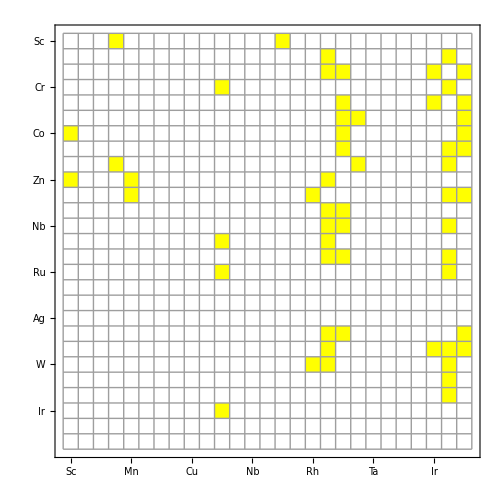

{2,2,2,-1,-1,-1,2,-1,1,2,2,2,-1,-1,2,-1,2,-1,-1,-1,-1,-1,1,1,2,2,1,-1,-1,2,-1,1,2,-1,2,2,2,1,1,2,1,2,2,1,-1,2,-1,1,-1,2,-1,1,2,-1,2,1,2}

{{1,4,2},{1,15,2},{2,18,2},{2,26,-1},{3,18,-1},{3,19,-1},{3,25,2},{3,27,-1},{4,11,1},{4,26,2},{5,19,2},{5,25,2},{5,27,-1},{6,19,-1},{6,20,2},{6,27,-1},{7,1,2},{7,19,-1},{7,27,-1},{8,19,-1},{8,26,-1},{8,27,-1},{9,4,1},{9,20,1},{9,26,2},{10,1,2},{10,5,1},{10,18,-1},{11,5,-1},{11,17,2},{11,26,-1},{11,27,1},{12,18,2},{12,19,-1},{13,18,2},{13,19,2},{13,26,2},{14,11,1},{14,18,1},{15,18,2},{15,19,1},{15,26,2},{16,11,2},{16,26,1},{20,18,-1},{20,19,2},{20,27,-1},{21,18,1},{21,25,-1},{21,26,2},{21,27,-1},{22,17,1},{22,18,2},{22,26,-1},{23,26,2},{24,26,1},{25,11,2}}

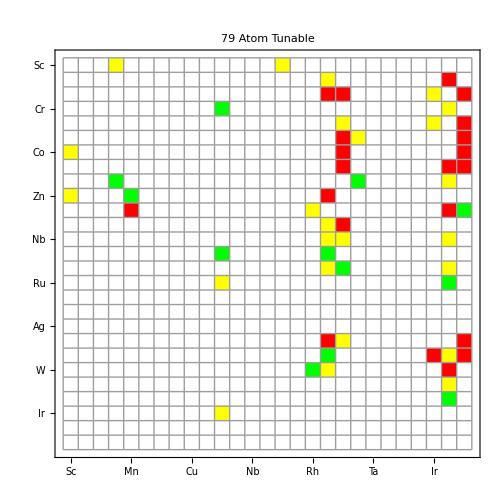

```mathematica
bigPairs = finalTunableadj[[All,1]] /.elementList
MatrixPlot[ SparseArray[ # -> 1, {27,27}] & @ bigPairs,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]



BigSeglst = assignNums[getBigSeg[#1,#2]]& @@@ bigPairs

myDataBigSeglst = Table[Insert[bigPairs[[i]],BigSeglst[[i]],3],{i,Length[BigSeglst] }]



MatrixPlot[ SparseArray[ # -> myDataBigSeglst[[All,3]], {27, 27} ] & @ bigPairs,ColorRules-> segColor,Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500, PlotLabel->"79 Atom Tunable"]
```

#### Format Data Table for export:

```mathematica
core = PrependTo[finalTunableadj[[All,1,1]], "  "];
finaltunableadja
```

finaltunableadja

## Final Figures:

-Graphics- -Graphics-

-Graphics- -Graphics-

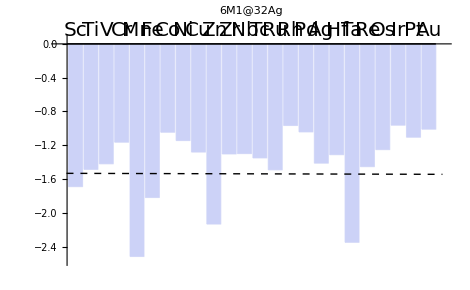
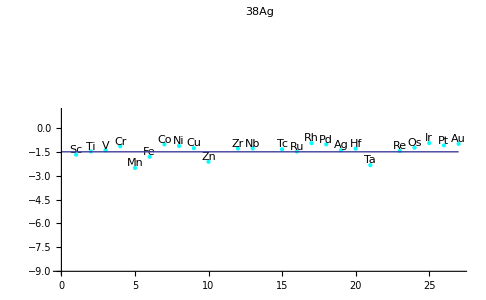
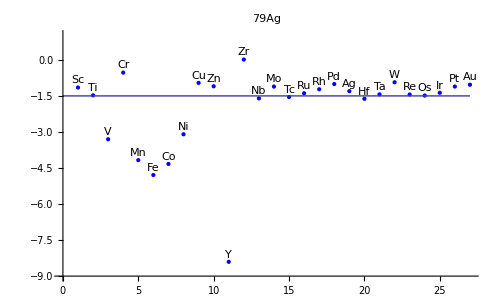
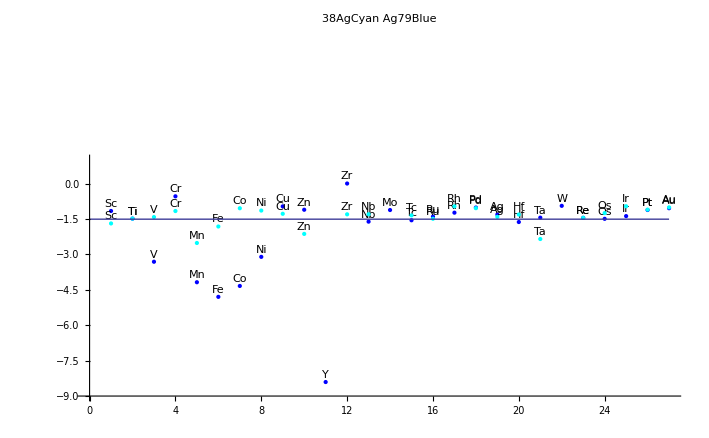
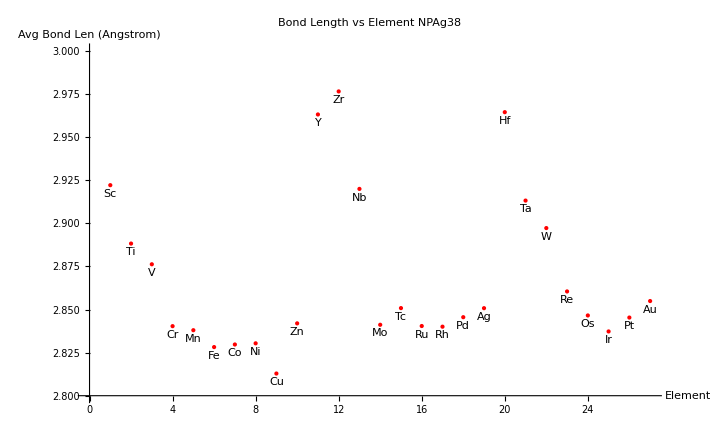
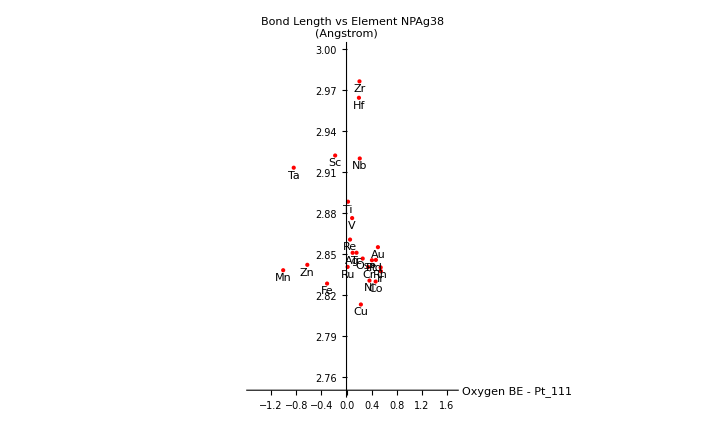
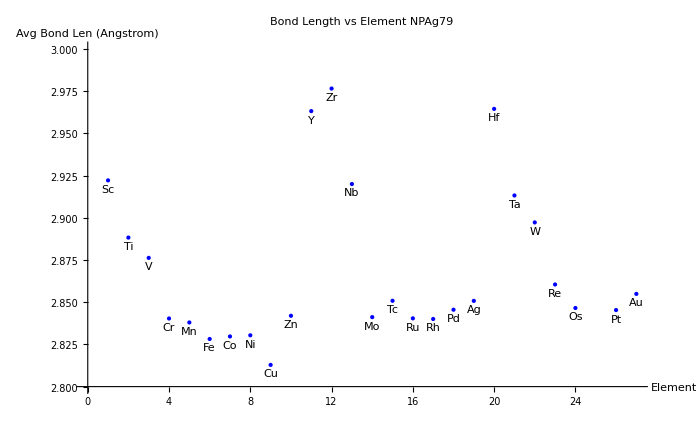
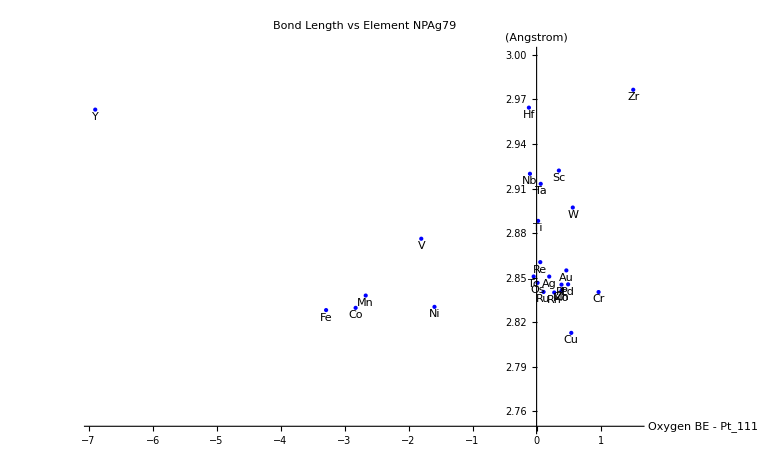
```mathematica
Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-
```

Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-

```mathematica
Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics-
```

Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics-

```mathematica
stackTest = {{1,2,3,4,5,6,7,8,9,10}}
```

{{1,2,3,4,5,6,7,8,9,10}}

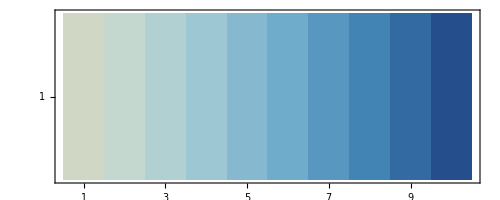

```mathematica
MatrixPlot[stackTest, ColorFunction->"RedBlueTones"]
```

```mathematica
Length[tunableORRData]
```

27

```mathematica
smallBindingTable
```

{{-6.732,-7.27517,-5.01151,-105.511,-9.4589,-7.59326,-9.36046,-3.41948,-6.79604,-4.47385,-28.8383,-87.6257,-123.857,-4.54772,-3.34368,-3.56681,-3.24293,-1.47187,-1.69071,-6.51991,-12.991,-5.28916,-180.394,-3.30855,-3.1094,-1.8083,-4.2198},{-6.57407,-6.3862,-5.45389,-4.65331,0.860106,-4.46683,-4.01216,-3.1242,-2.74773,-2.80093,-6.39748,-6.09923,-3.18594,-4.5779,-6.36042,-3.23825,-2.92423,-1.61127,-1.48652,-6.57345,-4.54179,-6.08298,-3.93447,-3.02605,-2.86587,-1.63843,-1.19295},{-6.54497,-6.53329,-6.0358,-4.78015,-6.37304,-4.20426,-3.80912,-3.1112,107.983,-3.46504,-11.9687,-6.03031,-5.06045,-3.96864,-4.90052,-3.07008,-2.81276,-1.60509,-1.42055,-5.76192,-5.01714,-6.96436,-5.20379,-2.96113,-3.26455,-1.87771,-1.10513},{-5.28476,-5.87817,-4.8642,-4.36083,-4.75426,-4.13973,-3.82682,-3.33217,4.34293,-3.2243,-9.61628,-5.80414,-5.41101,-4.79706,-4.55506,-3.06878,-2.69414,-1.7745,-1.16451,-10.9609,-5.70199,-6.50406,-5.03668,-2.9779,-3.33661,-2.29656,-0.131714},{-6.02304,-5.82231,-5.32531,-4.2108,-4.97377,3.10849,-3.88977,-3.03449,-30.2487,-4.1564,-6.57849,-5.88691,-4.79628,-4.70149,-4.63215,-3.24935,-1.55186,-1.90981,-2.51796,-9.72864,-5.1199,-5.64631,-5.04048,-3.07473,-2.71754,-1.29537,-1.21843},{-13.0879,-6.05419,-5.44884,-4.33451,-5.13699,-4.33105,-3.918,-3.95997,-84.9591,-4.12367,-6.33317,-6.38844,-5.32993,-4.90242,-4.78625,-3.41748,-2.88007,-1.79372,-1.81939,-6.33952,-5.42191,-5.80547,-5.06802,-3.41229,-2.99085,-1.54796,-1.44088},{-13.0006,-5.96781,-5.2165,-4.37512,-4.97284,-4.33114,-4.33615,-3.53216,-2.26743,-3.61848,-6.66744,-6.41409,-5.52062,-4.73777,-4.78966,-3.39506,-2.94096,-1.8705,-1.04659,0,-5.9382,-6.07371,-5.12424,-2.35279,5.22045,-2.23698,-1.30395},{-6.9298,-5.99329,-5.39335,-4.821,-6.24834,-4.45547,-3.98886,-3.58221,4.422,-4.38025,-6.57842,-5.59534,-5.20524,-5.14707,-5.0522,-3.47045,-3.00545,-2.5603,-1.14478,-12.637,-5.87252,-6.0438,-5.16825,-3.04447,-2.85679,-2.00655,-0.671956},{-10.1741,-6.27368,-6.19217,-8.31004,-17.3761,-4.63675,-4.22869,-3.66886,-2.55195,-3.60933,-6.14067,-7.95486,-4.96954,-4.30542,-4.72473,-3.64541,-3.12462,-2.05841,-1.2814,-6.63924,-4.56169,-5.68116,-4.60079,-3.29129,-3.06652,-2.07835,-1.51495},{-9.78975,-6.09903,-5.35288,-9.62582,-15.1995,-7.54962,-4.20816,-3.57802,-2.73171,-6.00803,-10.1792,-5.90802,-5.13033,-6.74419,-5.22573,-3.81919,-3.15717,-1.87809,-2.13397,-6.53378,-9.22608,-5.67645,-5.67967,-3.55864,-3.11476,-2.08233,-2.16209},{-6.8173,-7.14565,-7.95136,-90.5081,-7.72887,-8.45685,-10.5746,-7.59255,44.8605,0,-6.36134,-6.67835,-10.641,-541.025,-14.6376,-5.72627,-5.96966,-1.56194,-10.0711,-6.48629,-7.5176,-0.189288,1.19153,-19.0715,-3.75936,-7.98813,1.2205},{-6.63861,-6.65831,-3.98049,-1.90822,-5.1863,-16.6328,-8.84615,-3.28998,-6.2878,-4.81045,-6.10997,-5.89325,-4.2119,-3.89886,-4.14224,-3.41,-2.8825,-1.60735,-1.30394,-6.72428,-5.83372,-5.79673,-4.66692,-3.10247,-3.1188,-2.96714,-2.46874},{-6.62186,-6.6907,-5.11316,-4.22,-5.37438,-7.53593,-3.90362,-3.10452,136.641,-3.93171,-6.11813,-6.13659,-3.82354,-3.57326,-4.76024,-3.19129,-2.54989,-1.65592,-1.29924,-7.26422,-5.02008,-5.10755,-2.962,-3.00746,-2.75403,-1.77984,-1.087},{-6.48357,-6.36289,-5.46906,-4.84749,-4.55823,-4.44518,-3.91444,-3.17035,-3.58145,-3.30349,-1.99753,-4.60329,-2.44094,-3.94854,-4.54097,-3.07597,-2.55175,-1.92627,4.36713,-8.24918,-3.24031,-5.0098,-3.99774,-3.10698,-3.27815,-2.17434,-1.1764},{-6.46705,-6.3184,-5.59829,-4.1004,2.55369,-4.36603,-3.99099,-3.33538,-2.95589,-3.15032,-6.07776,-4.66455,-5.40433,-3.523,-4.5672,-3.28042,-2.68259,-2.46921,-1.35072,-5.1584,-5.81326,-4.88849,-4.88852,-3.39901,-3.00302,-3.48518,-0.922638},{-7.19689,-6.286,-6.16488,-4.23323,-4.55508,-4.6794,-4.16524,-3.60022,-2.64165,-5.50071,-11.8133,-5.63919,-5.16434,-3.73418,-4.55187,-3.34079,-2.7642,-2.04738,-1.49208,-5.78859,-5.51309,-5.43795,-4.92475,-3.57668,-2.95432,-2.03626,-0.787955},{-7.56776,-6.07736,-5.97566,-4.33796,-4.50586,-4.3043,-4.14986,-3.63601,-2.35353,-4.57655,-12.296,-5.62819,-5.39405,-3.83913,-4.68654,-3.29405,-2.83568,-2.13715,-0.966458,-6.29401,-5.50667,-5.94071,-4.85884,-3.22235,-3.1394,-2.07589,-0.482705},{-6.92467,-6.72004,-6.32581,-11.0014,-4.13434,4.43605,-4.37728,-3.73436,-2.41587,-6.62543,-12.0309,-5.7205,-6.39687,4.42889,-4.40312,-3.64166,-3.25703,-2.21809,-1.0429,-6.48135,-4.83744,-4.41985,-5.70304,-2.99609,-3.3895,-2.15726,-0.379127},{-6.84269,-6.26751,-5.42024,-3.71058,-19.9224,-10.6631,-14.2833,-8.85643,13.5035,-3.30866,-8.86033,-5.89122,-5.36625,6.03698,-4.29201,-3.84606,-3.41949,-2.23744,-1.41273,-6.48503,-5.86511,-5.06686,-3.53317,-2.8647,4.42182,-2.25204,-1.72996},{-6.61541,-7.55283,-4.92089,-6.99641,2.55403,-12.3982,-8.18252,-3.22926,-5.60863,-6.0927,-176.772,-6.06518,-5.80175,-4.04486,-9.05536,-3.31957,-2.81817,-1.62158,-1.31235,-6.42587,-7.46793,-7.5369,-4.86036,-3.00894,-3.05479,-1.63904,-1.63271},{-6.5904,-6.74637,-5.65934,-4.92189,-5.74707,-6.24705,-3.99528,-3.10146,-3.50936,-4.04648,-7.10375,-7.05281,-3.66082,-5.21088,-5.15964,-3.15559,-2.55747,-1.66047,-2.3501,-7.22216,-4.75924,-4.57433,-3.00234,-2.95792,-2.83783,-1.80795,-1.12029},{-6.42686,-6.21165,-5.05349,-4.29623,-4.54741,-4.46051,-3.86132,-3.16422,-197.533,-3.26868,-8.31362,-5.52697,-4.84873,-4.76133,-4.24107,-3.33038,-2.7658,-1.52766,4.42157,-5.87914,-4.5517,-6.11537,-4.05227,-3.36523,4.42193,-2.01085,-1.16135},{-12.4213,-5.65464,-5.17227,-4.68497,2.85118,2.20532,-3.96304,-3.20929,-3.13041,-3.20482,-13.1203,-4.54927,-5.74259,-3.5778,-4.61148,-3.31737,-2.68263,-1.85017,-1.45391,-4.80219,-6.08356,-4.97745,-4.88537,-3.41598,-3.52136,-1.22974,-1.04512},{-7.07662,4.23474,-5.80317,-4.26711,-4.55521,-4.67878,-3.9448,-3.53662,-2.64505,-2.97908,-7.04467,-5.08131,-5.15957,-3.85669,-4.54198,-3.45615,-2.96828,-2.01866,-1.25234,-5.48023,-4.93588,-5.48682,-5.1458,-3.31349,4.60888,-2.06396,-0.76104},{-6.61833,-6.36406,-5.35434,-4.53383,-4.70117,-4.74689,-4.03604,-3.59924,-2.31568,-4.46419,-12.1633,-5.88673,-5.45283,-4.14308,-4.92745,-3.59097,-3.08165,-2.10359,-0.963033,-6.26121,-6.0361,-5.51066,-5.25085,-3.47908,-3.06277,-2.09982,-0.578992},{-14.1286,4.42145,-5.43098,-4.9017,-4.17768,-6.60889,-5.15888,-3.6883,-2.07893,-2.38308,-13.1342,-5.63728,-5.19096,-4.33398,-5.11143,-3.63746,-3.24358,-2.14413,-1.10553,-6.2898,-5.69808,-4.53879,-5.70431,-3.4492,-3.46141,-2.25102,-0.593863},{-10.3259,-6.82941,-5.48113,-15.0043,-18.5632,-16.3959,-9.51913,-9.05336,1.15258,-3.50652,-12.1426,-6.15909,-4.79829,3.73948,-2.97537,-3.79717,-3.46909,-2.26438,-1.01026,-6.484,-5.94237,-4.68558,-12.2434,-1.87671,4.42182,-2.31682,-1.69444}}

```mathematica
Function[myTable, {tunableORRData = Replace[myTable ,a_/;Abs[a]≥10->0,{2}] - ORR /. targets;d=Sign@Diagonal@tunableORRData; returnValue[row_, col_,myTable] := myTable[[row,col]] ;tunablePairs = Position[(tunableORRDataᵀ d)ᵀ,_?Negative]  /. Reverse /@ elementList; pairEnergy = returnValue[#1, #2]& @@{#1,#2}&@@@Position[(tunableORRDataᵀ d)ᵀ,_?Negative] ;
tempVar = Partition[Riffle[tunablePairs, pairEnergy],2];
filterImposs = Replace[tempVar,a_/;Abs[a]≥5->0 ,{2}] ;
filterImposs = Replace[filterImposs,a_/;a > 1->0 ,{2}] ;
Cases[filterImposs,{x_,y_}/;y ≠ 0]}][#] & /@ {smallBindingTable, bigBindingTable}








(*Cases[tt,x_/;Abs[x[[1]]-x[[2]]]>3];*)
```

{{{}},{{}}}

```mathematica
tst = { {1,2,3}, {2,3,4}, {4,5,6} }
```

{{1,2,3},{2,3,4},{4,5,6}}

```mathematica
tst[[All,1]]
tst[[All,2]]
```

{1,2,4}

{2,3,5}

```mathematica
{2,3,5}
```

{2,3,5}

```mathematica
L[#]& @@{1}
```

L[1]

```mathematica
shit = { { {a,b},1,2 }, { {l,x},2,5 } }
```

{{{{{1,18},{1,19},{2,5},{2,27},{3,27},{4,9},{4,27},{5,6},{5,19},{5,26},{5,27},{6,19},{6,27},{7,27},{8,9},{8,27},{10,19},{11,22},{11,23},{11,27},{13,27},{14,27},{15,5},{15,27},{16,27},{17,27},{18,6},{18,14},{18,27},{19,25},{20,5},{21,19},{21,27},{22,25},{22,27},{23,5},{23,6},{23,26},{23,27},{24,2},{24,25},{24,27},{25,27},{26,2},{26,27},{27,9},{27,14},{27,25}},b},1,2},{{l,x},2,5}}

```mathematica
Thread[Append, shit ,{2}]
```

Append

```mathematica
m[[1]]
```

Part::partd: Part specification m ⟦ 1 ⟧ is longer than depth of object.

m⟦1⟧

```mathematica
bigSegTableOxygen⟦1,1⟧
```

0.00165928

```mathematica
a = {{1,18},{1,19},{2,5},{2,27},{3,27},{4,9},{4,27},{5,6},{5,19},{5,26},{5,27},{6,19},{6,27},{7,27},{8,9},{8,27},{10,19},{11,22},{11,23},{11,27},{13,27},{14,27},{15,5},{15,27},{16,27},{17,27},{18,6},{18,14},{18,27},{19,25},{20,5},{21,19},{21,27},{22,25},{22,27},{23,5},{23,6},{23,26},{23,27},{24,2},{24,25},{24,27},{25,27},{26,2},{26,27},{27,9},{27,14},{27,25}}
```

{{1,18},{1,19},{2,5},{2,27},{3,27},{4,9},{4,27},{5,6},{5,19},{5,26},{5,27},{6,19},{6,27},{7,27},{8,9},{8,27},{10,19},{11,22},{11,23},{11,27},{13,27},{14,27},{15,5},{15,27},{16,27},{17,27},{18,6},{18,14},{18,27},{19,25},{20,5},{21,19},{21,27},{22,25},{22,27},{23,5},{23,6},{23,26},{23,27},{24,2},{24,25},{24,27},{25,27},{26,2},{26,27},{27,9},{27,14},{27,25}}

```mathematica
mylst = assignNums[getBigSeg[#1,#2]]& @@@ a

Table[Insert[a[[i]],mylst[[i]],3],{i,Length[mylst] }]
```

{2,2,-1,2,-1,1,2,2,2,-1,-1,-1,-1,-1,2,-1,-1,-1,1,1,-1,2,-1,2,1,2,1,2,2,-1,2,2,-1,-1,1,2,-1,2,1,1,2,1,2,-1,2,2,2,2}

{{1,18,2},{1,19,2},{2,5,-1},{2,27,2},{3,27,-1},{4,9,1},{4,27,2},{5,6,2},{5,19,2},{5,26,-1},{5,27,-1},{6,19,-1},{6,27,-1},{7,27,-1},{8,9,2},{8,27,-1},{10,19,-1},{11,22,-1},{11,23,1},{11,27,1},{13,27,-1},{14,27,2},{15,5,-1},{15,27,2},{16,27,1},{17,27,2},{18,6,1},{18,14,2},{18,27,2},{19,25,-1},{20,5,2},{21,19,2},{21,27,-1},{22,25,-1},{22,27,1},{23,5,2},{23,6,-1},{23,26,2},{23,27,1},{24,2,1},{24,25,2},{24,27,1},{25,27,2},{26,2,-1},{26,27,2},{27,9,2},{27,14,2},{27,25,2}}